## NEC angle

```mathematica
(* EOMs in GG gauge *)
Eq15=-((-3+Dim) (-1+a[t,r]^2) f[t,r])/r+Derivative[0,1][f][t,r];
Eq16=1/(16 r)(8 (-3+Dim) a[t,r]^3-a[t,r] (8 (-3+Dim)+(-2+Dim)^3 Uu[t,r]^2+(-2+Dim)^3 Vv[t,r]^2)+16 r Derivative[0,1][a][t,r]);
Eq17=-1/2 (-3+Dim) a[t,r]^3+1/(16 r)a[t,r] (8 (-3+Dim) r+(-2+Dim)^3 (r+f[t,r]) Uu[t,r]^2+(-2+Dim)^3 (r-f[t,r]) Vv[t,r]^2)+Derivative[1,0][a][t,r];
Eq18=1/(8 (r+f[t,r]))(-2+Dim)^2 ⅇ^(-((-4+Dim) t)) r^(-5+Dim) (f[t,r] ((2-Dim+2 (-3+Dim) a[t,r]^2) Uu[t,r]-(-2+Dim) Vv[t,r]+2 r Derivative[0,1][Uu][t,r])+2 r (r Derivative[0,1][Uu][t,r]+Derivative[1,0][Uu][t,r]));
Eq19=1/(2 r (r-f[t,r]))(f[t,r] ((-2+Dim) Uu[t,r]+(-2+Dim-2 (-3+Dim) a[t,r]^2) Vv[t,r]-2 r Derivative[0,1][Vv][t,r])+2 r (r Derivative[0,1][Vv][t,r]+Derivative[1,0][Vv][t,r]));
EOMGG={Eq15,Eq16,Eq17,Eq18,Eq19};
```

```mathematica
(* EOMs with a replaced by inva=1/a^2 *)
assume={r>0,Dim>3,t>-Infinity};
replainva={a[t,r]->1/Sqrt[inva[t,r]],Derivative[0,1][a][t,r]->D[1/Sqrt[inva[t,r]],r], Derivative[1,0][a][t,r]->D[1/Sqrt[inva[t,r]],t]};
mult={1,-2inva[t,r]^(3/2),-2inva[t,r]^(3/2),1,1};
EOM=mult*EOMGG/.replainva//Simplify;
%//TableForm
```

-((-3+Dim) f[t,r] (-1+1/inva[t,r]))/r+f^(0,1)[t,r]
(24-8 Dim+inva[t,r] (8 (-3+Dim)+(-2+Dim)^3 Uu[t,r]^2+(-2+Dim)^3 Vv[t,r]^2)+8 r inva^(0,1)[t,r])/(8 r)
-3+Dim-(inva[t,r] (8 (-3+Dim) r+(-2+Dim)^3 (r+f[t,r]) Uu[t,r]^2+(-2+Dim)^3 (r-f[t,r]) Vv[t,r]^2))/(8 r)+inva^(1,0)[t,r]
((-2+Dim)^2 ⅇ^(-((-4+Dim) t)) r^(-5+Dim) (f[t,r] ((2-Dim+(2 (-3+Dim))/inva[t,r]) Uu[t,r]-(-2+Dim) Vv[t,r]+2 r Uu^(0,1)[t,r])+2 r (r Uu^(0,1)[t,r]+Uu^(1,0)[t,r])))/(8 (r+f[t,r]))
(f[t,r] ((-2+Dim) Uu[t,r]+(-2+Dim+(6-2 Dim)/inva[t,r]) Vv[t,r]-2 r Vv^(0,1)[t,r])+2 r (r Vv^(0,1)[t,r]+Vv^(1,0)[t,r]))/(2 r (r-f[t,r]))

```mathematica
(* series ansatz for the fields *)
Ord=5;
iser[t_,r_]:=Sum[r^i*Subscript[is, i][t],{i,0,Ord}];
fser[t_,r_]:=Sum[r^i*Subscript[fs, i][t],{i,0,Ord}];
Vser[t_,r_]:=Sum[r^i*Subscript[vs, i][t],{i,0,Ord}];
User[t_,r_]:=Sum[r^i*Subscript[us, i][t],{i,0,Ord}];
(* boundary condidtions *)
replBC={Subscript[is, 0]->(1&),Subscript[is, 1]->(0&),Subscript[fs, 1]->(0&),Subscript[vs, 0]->(0&),Subscript[vs, 1]->Subscript[ps, 1],Subscript[vs, 2]->Subscript[ps, 2],Subscript[us, 0]->(0&),Subscript[us, 1]->Subscript[ps, 1],Subscript[us, 2][t]->-Subscript[ps, 2][t]};
replser=Flatten[{inva->iser,f->fser,Vv->Vser,Uu->User,replBC}];
```

```mathematica
(* series expansion of the EOMs *)
EOMLO=Simplify[Series[EOM//.replser,{r,0,1}],Assumptions->assume]//Normal;
Solve[Thread[EOMLO[[;;]]==0],{Subscript[fs, 2][t],Subscript[is, 2][t],Subscript[ps, 2][t]}];
sol2=Flatten[{%,D[%,t]}]/.replBC//Simplify
```

{fs_2[t]→((-3+Dim) (-2+Dim)^3 fs_0[t] ps_1[t]^2)/(8 (-1+Dim)),is_2[t]→-((-2+Dim)^3 ps_1[t]^2)/(4 (-1+Dim)),ps_2[t]→(ps_1[t]+ps_1'[t])/((-1+Dim) fs_0[t]),fs_2'[t]→((-3+Dim) (-2+Dim)^3 ps_1[t] (ps_1[t] fs_0'[t]+2 fs_0[t] ps_1'[t]))/(8 (-1+Dim)),is_2'[t]→-((-2+Dim)^3 ps_1[t] ps_1'[t])/(2 (-1+Dim)),ps_2'[t]→(-ps_1[t] fs_0'[t]-fs_0'[t] ps_1'[t]+fs_0[t] (ps_1'[t]+ps_1''[t]))/((-1+Dim) fs_0[t]^2)}

```mathematica
(* linear ansatz for ps1 *)
ps1BC[t_]:=alpha0(t-t0);
replps1=Subscript[ps, 1]->ps1BC;
```

```mathematica
(* null vectors at the center *)
v1=Limit[Vser[t,r]/r/.replBC/.sol2/.replps1,r->0]//Simplify
v2=Limit[D[Vser[t,r]/r,r]/.replBC/.sol2/.replps1,r->0]/.t->t0//Simplify
u1=v1
u2=-v2
```

alpha0 (t-t0)

alpha0/((-1+Dim) fs_0[t0])

alpha0 (t-t0)

-alpha0/((-1+Dim) fs_0[t0])

```mathematica
(* NEC angle *)
NECline1=Normal[Series[v1+r v2,{t,t0,1}]];
NECline2=Normal[Series[u1+r u2,{t,t0,1}]];
vec1t=Solve[NECline1==0,t][[1]]/.r->1//Simplify;
vec2t=Solve[NECline2==0,t][[1]]/.r->1//Simplify;
Norm1=(t-t0/.vec1t)^2*(-Subscript[fs, 0][t0]^2)+1//Simplify;
Norm2=(t-t0/.vec2t)^2*(-Subscript[fs, 0][t0]^2)+1//Simplify;
inner12=(t-t0/.vec1t)*(t-t0/.vec2t)(-Subscript[fs, 0][t0]^2)+1//Simplify;
coshNEC=Assuming[Dim>3,inner12/Sqrt[Norm1 Norm2]//Simplify]
replNEC=FullSimplify[Solve[Cosh[NEC]==coshNEC,NEC][[2]]/.C[1]->0,assume]
```

(2-2 Dim+Dim^2)/((-2+Dim) Dim)

{NEC→Log[Dim/(-2+Dim)]}

```mathematica
(* large D limit *)
Normal[Series[NEC/.replNEC,{Dim,Infinity,1}]//Simplify]
```

2/Dim

```mathematica
(* small D limit *)
Normal[Series[NEC/.replNEC/.Dim->3+eps,{eps,0,1}]//Simplify]//FullSimplify
```

-(2 eps)/3+Log[3]

```mathematica
(* D=4 result *)
NEC/.replNEC/.Dim->4//FullSimplify
```

Log[2]

alpha==Gudermannian[Log[Dim/(-2+Dim)]]

2/Dim

-2/5 (-3+Dim)+2 ArcCot[2]

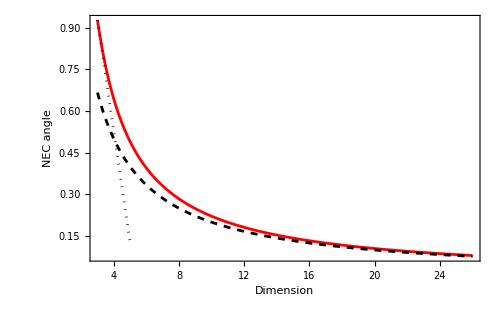

```mathematica
(* two equivalent ways to write the geometric NEC angle *)
alpha[Dim_]=Gudermannian[NEC]/.replNEC;
FullSimplify[2ArcTan[Tanh[NEC/2]]==alpha/.replNEC//FunctionExpand,Assumptions->assume]
(* large D limit *)
alphaLD[Dim_]=Series[alpha[Dim],{Dim,Infinity,1}]//Normal
(* small D limit *)
alphaSD[Dim_]=FullSimplify[Series[alpha[Dim],{Dim,3,1}],Assumptions->assume]//Normal
Show[
Plot[alpha[Dim],{Dim,3,26},PlotStyle->Red,PlotRange->All],
Plot[alphaSD[Dim],{Dim,3,5},PlotStyle->{Black,Dotted}],
Plot[alphaLD[Dim],{Dim,3,26},PlotStyle->{Black,Dashed}]
,PlotRange->All,ImageSize->500,BaseStyle->20,Frame->True,FrameLabel->{"Dimension","NEC angle"}]
```

## Checking Equations

```mathematica
(* Ricci scalar *)
xmu={t,x,th,ph};
d=Length[xmu];
metric =Exp[-2 t]{ Exp[w[t,x]]{(x^2-f[t,x]^2),-x,0,0}, Exp[w[t,x]]{-x,1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[th]^2}};
metricinv=Inverse[metric];
g=Det[metric];
metric//MatrixForm
```

(ⅇ^(-2 t+w[t,x]) (x^2-f[t,x]^2) | -ⅇ^(-2 t+w[t,x]) x | 0 | 0
-ⅇ^(-2 t+w[t,x]) x | ⅇ^(-2 t+w[t,x]) | 0 | 0
0 | 0 | ⅇ^(-2 t) x^2 | 0
0 | 0 | 0 | ⅇ^(-2 t) x^2 Sin[th]^2)

```mathematica
(* Christoffel symbol and contraction *)
Gudd=Table[Sum[1/2metricinv[[i,l]](D[metric[[k,l]],xmu[[j]]]+D[metric[[j,l]],xmu[[k]]]-D[metric[[j,k]],xmu[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k,1,d}];
GGuddd=Table[Sum[Gudd[[i,j,m]]*Gudd[[m,k,l]],{m,1,d}],{i,1,d},{j,1,d},{k,1,d},{l,1,d}];
```

```mathematica
(* Riemann tensor, Ricci tensor and Ricci scalar *)
Ruddd=Table[D[Gudd[[i,l,j]],xmu[[k]]]-D[Gudd[[i,k,j]],xmu[[l]]]+GGuddd[[i,k,l,j]]-GGuddd[[i,l,k,j]],{i,1,d},{j,1,d},{k,1,d},{l,1,d}];
Rdd=Table[Sum[Ruddd[[m,i,m,j]],{m,1,d}],{i,1,d},{j,1,d}]//Simplify;
Rud=Table[Sum[metricinv[[i,m]]*Rdd[[m,j]],{m,1,d}],{i,1,d},{j,1,d}]//Simplify;
Rscal=Sum[Rud[[m,m]],{m,1,d}]//Simplify;
```

```mathematica
Rscal//Simplify
```

1/(x^2 f[t,x]^3)ⅇ^(2 t-w[t,x]) (-x f[t,x]^2 (f^(0,1)[t,x] (4+x w^(0,1)[t,x])+2 x f^(0,2)[t,x])+f[t,x]^3 (-2+2 ⅇ^w[t,x]-x^2 w^(0,2)[t,x])-x^2 (x f^(0,1)[t,x]+f^(1,0)[t,x]) (x w^(0,1)[t,x]+w^(1,0)[t,x])+x^2 f[t,x] (2 x w^(0,1)[t,x]+x^2 w^(0,2)[t,x]+w^(1,0)[t,x]+2 x w^(1,1)[t,x]+w^(2,0)[t,x]))

```mathematica
check13=Series[Rscal,{x,0,-1}]//Normal//FullSimplify
```

(2 ⅇ^(2 t-w[t,0]) (-2 x f^(0,1)[t,0]+f[t,0] (-1+ⅇ^w[t,0]+x w^(0,1)[t,0])))/(x^2 f[t,0])

```mathematica
(* Daniels Eq.13 *)
Eq13=(1-Exp[-w[t,0]])(dim-2)(dim-3)Exp[2t]/x^2+Exp[-w[t,0]]((dim-3) Derivative[0,1][w][t,0] -2(Derivative[0,1][f][t,0])/f[t,0])(dim-2)Exp[2t]/x//Simplify
```

((-2+dim) ⅇ^(2 t-w[t,0]) (-2 x f^(0,1)[t,0]+(-3+dim) f[t,0] (-1+ⅇ^w[t,0]+x w^(0,1)[t,0])))/(x^2 f[t,0])

```mathematica
check13==Eq13/.dim->4//Simplify
```

True

## 2D plot of Ricci scalar

```mathematica
SetDirectory[NotebookDirectory[]];
<<"shoot2.wl"
<<"plotter2.wl"
(* enlarges machine precision to numPrec digits *)  
round[x_,precc_:numPrec]:=If[  NumberQ[x],   Round[x,10^-precc],x]; 
(* if numeric rounds the expression up to the order given by precgoal *)
round[a_ b_,c_ ]:=round[a,c] round[b,c];
round[a_/b_,c_ ]:=round[a,c]/round[b,c];
round[a_+b_,c_ ]:=round[a,c]+round[b,c];
(* this is required to make the function automatically thread over a list *)
Attributes[round]={Listable};
(* Newton loop for mismatch of function values *)
iterateplot[plotfile_,Xini_,Nt_,dim_,xgrid_,xmatch_?NumericQ,epsVar_?NumericQ,delta_?NumericQ,Nnewton_?NumericQ]:=Module[{Xinow,solList,tnow,fL,fR,UL,UR,PsiL,PsiR,Minow,sol0,sol1,medMnow,TJacobian,ttotal,Xnow,tNow,Mnow,delX,delX0,X1,jacerr,plotNow},
(* initial conditions *)
Xinow=Xini;
solList={};
Print["#######################"];
Print["Solving initial guess."];
Print["#######################"];
tnow=AbsoluteTiming[{fL,fR,UL,UR,PsiL,PsiR,Minow}=shootplot[Xinow,xgrid,xmatch,Nt,dim,stepprec,maxits,False,plotfile];][[1]];
medMnow=Median[Abs[Minow]];
AppendTo[solList,Xinow];
Print["mismatch=",medMnow,", time=",tnow];
Print[{
ListPlot[{fL,fR},Joined->True,PlotStyle->{{Red},{Blue,Dashed}},ImageSize->300,InterpolationOrder->2,
Frame->True,Axes->False,
FrameLabel->{"τ","f(τ,x_match)"},
PlotLegends->Placed[{"f_left","f_right"},{0.4,0.75}],
LabelStyle->{Black,12,FontFamily->"Latin Modern Roman"},
PlotLabel->"x_match="<>ToString[xmatch//N]<>", Δ="<>ToString[Xinow[[-1,1]]]
],
ListPlot[{UL,UR},Joined->True,PlotStyle->{{Red},{Blue,Dashed}},ImageSize->300,InterpolationOrder->2,
Frame->True,Axes->False,
FrameLabel->{"τ","U(τ,x_match)"},
PlotLegends->Placed[{"U_left","U_right"},{0.4,0.75}],
LabelStyle->{Black,12,FontFamily->"Latin Modern Roman"},
PlotLabel->"x_match="<>ToString[xmatch//N]<>", Δ="<>ToString[Xinow[[-1,1]]]
],
ListPlot[{PsiL,PsiR},Joined->True,PlotRange->All,PlotStyle->{{Red},{Blue,Dashed}},ImageSize->300,InterpolationOrder->2,
Frame->True,Axes->False,
FrameLabel->{"τ","ψ(τ,x_match)"},
PlotLegends->Placed[{"ψ_left","ψ_right"},{0.4,0.75}],
LabelStyle->{Black,12,FontFamily->"Latin Modern Roman"},
PlotLabel->"x_match="<>ToString[xmatch//N]<>", Δ="<>ToString[Xinow[[-1,1]]]
],
Show[
LogPlot[medMnow,{x,1,Length[Minow]},PlotStyle->{Red}
,ImageSize->300,PlotStyle->Red,Frame->True,Axes->False,PlotRange->{{0,Length[Minow]},{10^(MantissaExponent[medMnow][[2]]-2),10^(MantissaExponent[medMnow][[2]]+2)}},
FrameLabel->{"pnt","|M|"},
PlotLegends->Placed[{"median|M|"},{0.4,0.85}],
LabelStyle->{Black,12,FontFamily->"Latin Modern Roman"},
PlotLabel->"median|M|="<>ToString[medMnow,FortranForm],GridLines->{{{Nt/2,Directive[Black,Dashed]},{Nt,Directive[Black,Dashed]},{(3Nt)/2,Directive[Black,Dashed]}},None}]
,ListLogPlot[Abs[Minow[[;;]]],PlotStyle->Blue],Graphics[Text["Δf",{Nt/4,Log[10^(MantissaExponent[medMnow][[2]]+0.8)]}]],Graphics[Text["ΔU",{(3Nt)/4,Log[10^(MantissaExponent[medMnow][[2]]+0.8)]}]],Graphics[Text["ΔΨ",{(5Nt)/4,Log[10^(MantissaExponent[medMnow][[2]]+0.8)]}]]]}
];
];
plotfun[plotfile_,xgrid_,Xini_,Nt_,imatch_,dim_]:=Module[{solL,solR,Nplot,stepL,stepR,fL,aL,uL,psiL,fR,aR,uR,psiR,funnow,funmatch(*,
datafR,dataaR,datauR,datapsiR,datafL,dataaL,datauL,datapsiL*)},
(*Get solution*)
{solL,solR}=Get[plotfile];
(*parameters for plots*)
Nplot=50;
stepL=Floor[Length[solL]/Nplot];
stepR=Floor[Length[solR]/Nplot];
(*Build tables for plots L*)
fL={};
aL={};
uL={};
psiL={};

Do[funnow=reconstFunctionplot[solL[[i]],xgrid[[i]],Xini[[-1,1]],Nt,dim,False];
AppendTo[fL,Table[{xgrid[[i]],funnow[[1,j,1]],funnow[[1,j,2]]},{j,1,Nt}]];
AppendTo[aL,Table[{xgrid[[i]],funnow[[2,j,1]],funnow[[2,j,2]]},{j,1,Nt}]];
AppendTo[uL,Table[{xgrid[[i]],funnow[[3,j,1]],funnow[[3,j,2]]},{j,1,Nt}]];
AppendTo[psiL,Table[{xgrid[[i]],funnow[[4,j,1]],funnow[[4,j,2]]},{j,1,Nt}]];
,{i,1,Length[solL],stepL}];

funmatch=reconstFunctionplot[solL[[imatch]],xgrid[[imatch]],Xini[[-1,1]],Nt,dim,False];

datafL=Flatten[AppendTo[fL,Table[{xgrid[[imatch]],funmatch[[1,j,1]],funmatch[[1,j,2]]},{j,1,Nt}]],1];
dataaL=Flatten[AppendTo[aL,Table[{xgrid[[imatch]],funmatch[[2,j,1]],funmatch[[2,j,2]]},{j,1,Nt}]],1];
datauL=Flatten[AppendTo[uL,Table[{xgrid[[imatch]],funmatch[[3,j,1]],funmatch[[3,j,2]]},{j,1,Nt}]],1];
datapsiL=Flatten[AppendTo[psiL,Table[{xgrid[[imatch]],funmatch[[4,j,1]],funmatch[[4,j,2]]},{j,1,Nt}]],1];
(*Build tables for plots R*)
fR={};
aR={};
uR={};
psiR={};

Do[funnow=reconstFunctionplot[solR[[i]],xgrid[[-i]],Xini[[-1,1]],Nt,dim,False];
AppendTo[fR,Table[{xgrid[[-i]],funnow[[1,j,1]],funnow[[1,j,2]]},{j,1,Nt}]];
AppendTo[aR,Table[{xgrid[[-i]],funnow[[2,j,1]],funnow[[2,j,2]]},{j,1,Nt}]];
AppendTo[uR,Table[{xgrid[[-i]],funnow[[3,j,1]],funnow[[3,j,2]]},{j,1,Nt}]];
AppendTo[psiR,Table[{xgrid[[-i]],funnow[[4,j,1]],funnow[[4,j,2]]},{j,1,Nt}]];
,{i,1,Length[solR],stepR}];

funmatch=reconstFunctionplot[solR[[-1]],xgrid[[imatch]],Xini[[-1,1]],Nt,dim,False];

datafR=Flatten[AppendTo[fR,Table[{xgrid[[imatch]],funmatch[[1,j,1]],funmatch[[1,j,2]]},{j,1,Nt}]],1];
dataaR=Flatten[AppendTo[aR,Table[{xgrid[[imatch]],funmatch[[2,j,1]],funmatch[[2,j,2]]},{j,1,Nt}]],1];
datauR=Flatten[AppendTo[uR,Table[{xgrid[[imatch]],funmatch[[3,j,1]],funmatch[[3,j,2]]},{j,1,Nt}]],1];
datapsiR=Flatten[AppendTo[psiR,Table[{xgrid[[imatch]],funmatch[[4,j,1]],funmatch[[4,j,2]]},{j,1,Nt}]],1];

Print[GraphicsRow[{ListPlot3D[{datafL,datafR},PlotRange->All,AxesLabel->{"x","t","f[t,x]"},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman"},ImageSize->300,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],Mesh->None],ListPlot3D[{dataaL,dataaR},PlotRange->All,AxesLabel->{"x","t","a[t,x]"},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman"},ImageSize->300,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],Mesh->None],ListPlot3D[{datauL,datauR},PlotRange->All,AxesLabel->{"x","t","U[t,x]"},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman"},ImageSize->300,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],Mesh->None],ListPlot3D[{datapsiL,datapsiR},PlotRange->All,AxesLabel->{"x","t","Ψ[t,x]"},LabelStyle->{Black,16,FontFamily->"Latin Modern Roman"},ImageSize->300,ColorFunction->Function[{x,y,z},Hue[.65(1-z)]],Mesh->None]},ImageSize->1400]];
];
```

732

0.0016117

#######################

Solving initial guess.

#######################

mismatch=0.00270805, time=20.9685

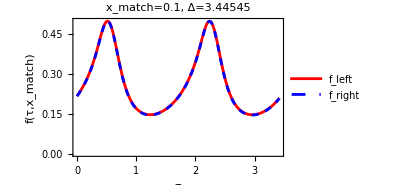
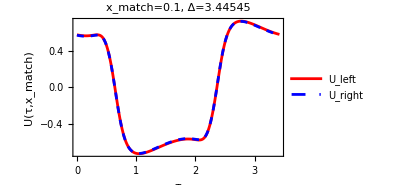
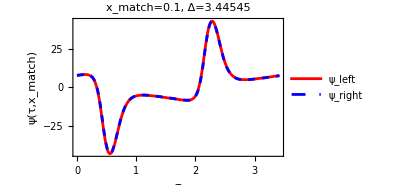
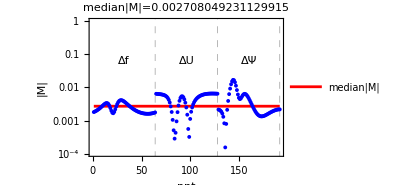

```mathematica
(* D=4 data *)
dim=round[4.000];
Nz=2500;
(* Define spatial domain according to GG-paper, with Subscript[x, c]=0, Subscript[x, p]=1 *)
xcut0=10/10000;
xmatch=1/10;
xcut1=9999/10000;
(*logarithmic grid for shooting*)
zcut0=Log[xcut0/(1-xcut0)]//N;
zcut1=Log[xcut1/(1-xcut1)]//N;
zmatch=Log[xmatch/(1-xmatch)]//N;
zgrid=Range[zcut0,zcut1,(zcut1-zcut0)/Nz];
xgrid=Exp[zgrid]/(1+Exp[zgrid]);
(*Position of matching surface in xgrid*)
imatch=PositionSmallest[Abs[xgrid-xmatch]][[1]]
(*The maximal step size in the xgrid, GG choose Nz~5000 such that h = 7*10^-4 *)
h=Max[Table[xgrid[[i]]-xgrid[[i-1]],{i,2,Length[xgrid]}]]
(*Set precision and max number of iterations for implicit step*)
stepprec=10^-12;
maxits=200;
epsVar=10^-8;
delta=1;
Nnewton=6;
numPrec=16;
(*Number of modes used in t-direction*)
Nt=128;
Xini=Get["dim4.0000.res"][[-1]];
plotfile="plot4.0000.res";
iterateplot[plotfile,Xini,Nt,dim,xgrid,xmatch,epsVar,delta,0];
```

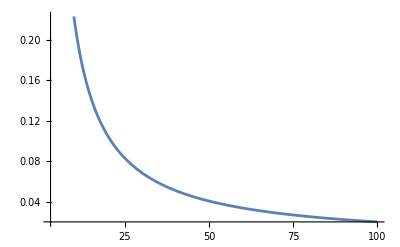

```mathematica
Plot[2 ArcCot[dim−1],{dim,3,100}]
```

```mathematica
plotfun[plotfile,xgrid,Xini,Nt,imatch,dim]
```

-Graphics-

```mathematica
(* building interpolating functions *)
dataf0=SortBy[Join[datafL[[;;-129]],datafR],First];
dataf=Table[{dataf0[[i,{1,2}]],dataf0[[i,3]]},{i,Length[dataf0]}];
dataU0=SortBy[Join[datauL[[;;-129]],datauR],First];
dataU=Table[{dataU0[[i,{1,2}]],dataU0[[i,3]]},{i,Length[dataU0]}];
dataa0=SortBy[Join[dataaL[[;;-129]],dataaR],First];
dataa=Table[{dataa0[[i,{1,2}]],dataa0[[i,3]]},{i,Length[dataa0]}];
datapsi0=SortBy[Join[datapsiL[[;;-129]],datapsiR],First];
datapsi=Table[{datapsi0[[i,{1,2}]],datapsi0[[i,3]]},{i,Length[datapsi0]}];
fint=Interpolation[dataf,InterpolationOrder->2];
Uint=Interpolation[dataU,InterpolationOrder->2];
aint=Interpolation[dataa,InterpolationOrder->2];
psiint=Interpolation[datapsi,InterpolationOrder->2];
Vint[x_,t_]=2x^2 psiint[x,t]+Uint[x,t];
Ricci[x_,t_]=-(dim-2)Exp[2t]Uint[x,t]*Vint[x,t]/(aint[x,t]*x)^2;
NEC[x_,t_]=Uint[x,t]*Vint[x,t]/x^2;
xmin=datafL[[1,1]]
xmax=datafR[[1,1]]
DeltaNow=datafR[[-1,2]]
```

0.001

0.9999

3.41853

```mathematica
DeltaNow
```

3.41853

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

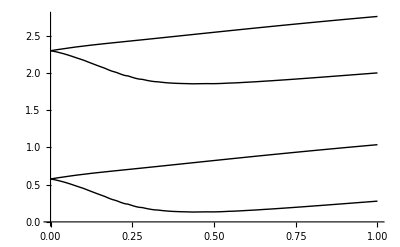

```mathematica
(* locating zero branches of Ricci scalar *)
xList=Range[xmin,xmax,0.001];
tList=Range[0,DeltaNow,0.001];
tbranch1=Table[t/.FindRoot[Ricci[x,t],{t,2.3,2.8}],{x,xList}];
tbranch2=Table[t/.FindRoot[Ricci[x,t],{t,1.7,2.3}],{x,xList}];
tbranch3=Table[t/.FindRoot[Ricci[x,t],{t,0.585,1.1}],{x,xList}];
tbranch4=Table[t/.FindRoot[Ricci[x,t],{t,0.1,0.58}],{x,xList}];
branch1int=Interpolation[Thread[{xList[[;;;;4]],tbranch1[[;;;;4]]}],InterpolationOrder->2];
branch2int=Interpolation[Thread[{xList[[;;;;4]],tbranch2[[;;;;4]]}],InterpolationOrder->2];
branch3int=Interpolation[Thread[{xList[[;;;;4]],tbranch3[[;;;;4]]}],InterpolationOrder->2];
branch4int=Interpolation[Thread[{xList[[;;;;4]],tbranch4[[;;;;4]]}],InterpolationOrder->2];
Plot[{branch1int[x],branch2int[x],branch3int[x],branch4int[x]},{x,0,1},PlotStyle->{{Thick,Black}}]
```

```mathematica
exportList=Thread[{xList[[;;]],tbranch1[[;;]],tbranch2[[;;]],tbranch3[[;;]],tbranch4[[;;]]}];
```

```mathematica
Export["NEClines.dat",exportList,"Data"]
```

NEClines.dat

```mathematica
Filling
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

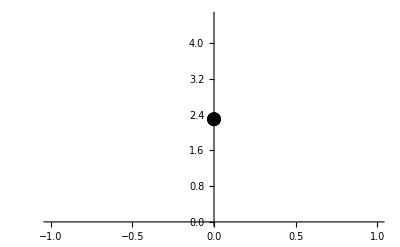

```mathematica
ListPlot[{{0,branch1int[0]}},PlotStyle->{PointSize[0.025],Black}]
```

```mathematica
NotebookDirectory[]
```

/home/ecker/Dropbox/CriticalCollapse/Formulas/

```mathematica
p1=Show[
Plot[{branch1int[x],branch2int[x],branch3int[x],branch4int[x]},{x,0,1},
Filling->{1->{{2},Lighter[Lighter[Red]]},2->{{3},Lighter[Lighter[Blue]]},3->{{4},Lighter[Lighter[Red]]},1->{Top,Lighter[Lighter[Blue]]}
,4->{Bottom,Lighter[Lighter[Blue]]}
},
PlotStyle->{{Thick,Black}},Frame->True,PlotRangePadding->None,FrameLabel->{"x","τ"},PlotRange->{{0,1},{0,DeltaNow}},
LabelStyle->Directive[16,Black,FontFamily->"Latin Modern Roman"],AspectRatio->2/3,
Epilog->{
Text[Style["R<0",20,Darker[Blue],FontFamily->"Latin Modern Roman"],{0.5,1.4}],
Text[Style["R>0",20,Darker[Red],FontFamily->"Latin Modern Roman"],{0.5,2.2}]}
],
Plot[branch1int[xmin]+x*branch1int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],White,Dashed}],
Plot[branch2int[xmin]+x*branch2int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],White,Dashed}],
Plot[branch3int[xmin]+x*branch3int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],White,Dashed}],
Plot[branch4int[xmin]+x*branch4int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],White,Dashed}],
ListPlot[{{0,branch1int[0]}},PlotStyle->{PointSize[0.025],Black}],
ListPlot[{{0,branch4int[0]}},PlotStyle->{PointSize[0.025],Black}]
]
```

```mathematica
{branch4int[xmin]+x*branch4int'[xmin]}
{branch3int[xmin]+x*branch3int'[xmin]}
{branch2int[xmin]+x*branch2int'[xmin]}
{branch1int[xmin]+x*branch1int'[xmin]}
```

{0.577053-0.859563 x}

{0.577053+0.769894 x}

{2.29978-0.859563 x}

{2.29978+0.769894 x}

```mathematica
SetDirectory[NotebookDirectory[]]
Export["RicciD4.pdf",p1]
```

/home/ecker/Dropbox/CriticalCollapse/Formulas

RicciD4.pdf

```mathematica
xList
```

{0.001,0.006,0.011,0.016,0.021,0.026,0.031,0.036,0.041,0.046,0.051,0.056,0.061,0.066,0.071,0.076,0.081,0.086,0.091,0.096,0.101,0.106,0.111,0.116,0.121,0.126,0.131,0.136,0.141,0.146,0.151,0.156,0.161,0.166,0.171,0.176,0.181,0.186,0.191,0.196,0.201,0.206,0.211,0.216,0.221,0.226,0.231,0.236,0.241,0.246,0.251,0.256,0.261,0.266,0.271,0.276,0.281,0.286,0.291,0.296,0.301,0.306,0.311,0.316,0.321,0.326,0.331,0.336,0.341,0.346,0.351,0.356,0.361,0.366,0.371,0.376,0.381,0.386,0.391,0.396,0.401,0.406,0.411,0.416,0.421,0.426,0.431,0.436,0.441,0.446,0.451,0.456,0.461,0.466,0.471,0.476,0.481,0.486,0.491,0.496,0.501,0.506,0.511,0.516,0.521,0.526,0.531,0.536,0.541,0.546,0.551,0.556,0.561,0.566,0.571,0.576,0.581,0.586,0.591,0.596,0.601,0.606,0.611,0.616,0.621,0.626,0.631,0.636,0.641,0.646,0.651,0.656,0.661,0.666,0.671,0.676,0.681,0.686,0.691,0.696,0.701,0.706,0.711,0.716,0.721,0.726,0.731,0.736,0.741,0.746,0.751,0.756,0.761,0.766,0.771,0.776,0.781,0.786,0.791,0.796,0.801,0.806,0.811,0.816,0.821,0.826,0.831,0.836,0.841,0.846,0.851,0.856,0.861,0.866,0.871,0.876,0.881,0.886,0.891,0.896,0.901,0.906,0.911,0.916,0.921,0.926,0.931,0.936,0.941,0.946,0.951,0.956,0.961,0.966,0.971,0.976,0.981,0.986,0.991,0.996}

```mathematica
tList//Length
```

684

```mathematica
Table[{x,t,Ricci[x,t]//Chop},{x,xList},{t,tList}]//Dimensions
```

{200,684,3}

```mathematica
(* evaluating the original Ricci scalar expression is slow, so we re-interpolate on a new uniform grid *)
RicciList=Flatten[Table[{x,t,Ricci[x,t]},{x,xList},{t,tList}],1];
RicciInt=Interpolation[RicciList,InterpolationOrder->2]
xListExport=Subdivide[xmin,xmax,2000];
tListExport=Subdivide[0,DeltaNow,2000];
RicciList=Flatten[Table[{x,t,Ricci[x,t]},{x,xListExport},{t,tListExport}],1];
```

InterpolatingFunction[{{0.001, 0.999}, {0., 3.418}}, <>]

```mathematica
(* rescaled tau axis *)
tau0=branch3int[xmin]
scale=fint[xmin,tau0]
RicciListScale=Flatten[Table[{x,scale*t,Ricci[x,t]},{x,xListExport},{t,tListExport}],1];
```

0.577053

0.440516

```mathematica
NotebookDirectory[]
```

/home/ecker/Dropbox/CriticalCollapse/Formulas/

```mathematica
Export["Ricci4Dfine.dat",RicciList,"Data"]
```

Ricci4Dfine.dat

```mathematica
scale
```

0.440516

```mathematica
Export["Ricci4Dscale.dat",RicciListScale,"Data"]
```

Ricci4Dscale.dat

```mathematica
Export["Ricci4D.dat",RicciList,"Data"]
```

```mathematica
branch1export=Table[{x,branch1int[x]},{x,xListExport}];
branch2export=Table[{x,branch2int[x]},{x,xListExport}];
branch3export=Table[{x,branch3int[x]},{x,xListExport}];
branch4export=Table[{x,branch4int[x]},{x,xListExport}];
```

```mathematica
Export["branch1.dat",branch1export,"Data"]
Export["branch2.dat",branch2export,"Data"]
Export["branch3.dat",branch3export,"Data"]
Export["branch4.dat",branch4export,"Data"]
```

branch1.dat

branch2.dat

branch3.dat

branch4.dat

```mathematica
xListExport//Length
```

201

```mathematica
RicciList//Dimensions
```

{241001,3}

```mathematica
tan a= y/x
```

```mathematica
Table[{x,x*Tan[37/180]},{x,0,1,0.1}]
```

{{0.,0.},{0.1,0.02085},{0.2,0.0417001},{0.3,0.0625501},{0.4,0.0834002},{0.5,0.10425},{0.6,0.1251},{0.7,0.14595},{0.8,0.1668},{0.9,0.18765},{1.,0.2085}}

```mathematica
Export["Ricci4D.dat",RicciList,"Data"]
```

Ricci4D.dat

```mathematica
p1=Show[
ContourPlot[Ricci[x,y],{x,xmin,xmax},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",PlotRange->{{0,1},{0,DeltaNow},{-300,300}},Contours->14,ContourStyle->Black
,PlotRangePadding->None,Mesh->None,Frame->True,FrameLabel->{"x","τ"},ClippingStyle->{Blue,Darker[Red]},
(*,PlotLabel->"Ricci Scalar in D=4",*)
LabelStyle->Directive[16,Black],PlotLegends->Automatic
],
Plot[branch1int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch2int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch3int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch4int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch1int[xmin]+x*branch1int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch2int[xmin]+x*branch2int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch3int[xmin]+x*branch3int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch4int[xmin]+x*branch4int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}]
]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
Export["plot1.png",p1,ImageResolution->500]
```

plot1.png

```mathematica
600/14
```

300/7

```mathematica
p2=Show[
Plot3D[Ricci[x,y],{x,xmin,xmax},{y,0,DeltaNow},PlotRange->{{0,1},{0,DeltaNow},{-160,160}},ClippingStyle->{None,None},PlotPoints->400,(*ColorFunction->"TemperatureMap",*)LabelStyle->Directive[16,Black],PlotLegends->Automatic,Boxed->False,Mesh->False,PlotStyle->Directive[Opacity[0.7]],AxesLabel->{"x","τ","R"},AxesEdge->{{-1,-1},{1,-1},{-1,-1}},MaxRecursion->10,ViewPoint->{20, -20, 30}],
ParametricPlot3D[{x,branch1int[x],0},{x,0,1},PlotStyle->{Thickness[0.006],Black}],
ParametricPlot3D[{x,branch2int[x],0},{x,0,1},PlotStyle->{Thickness[0.006],Black}],
ParametricPlot3D[{x,branch3int[x],0},{x,0,1},PlotStyle->{Thickness[0.006],Black}],
ParametricPlot3D[{x,branch4int[x],0},{x,0,1},PlotStyle->{Thickness[0.006],Black}],
ParametricPlot3D[{x,branch1int[xmin]+x*branch1int'[xmin],0},{x,0,0.3},PlotStyle->{Thickness[0.006],Red,Dashed}],
ParametricPlot3D[{x,branch2int[xmin]+x*branch2int'[xmin],0},{x,0,0.3},PlotStyle->{Thickness[0.006],Red,Dashed}],
ParametricPlot3D[{x,branch3int[xmin]+x*branch3int'[xmin],0},{x,0,0.3},PlotStyle->{Thickness[0.006],Red,Dashed}],
ParametricPlot3D[{x,branch4int[xmin]+x*branch4int'[xmin],0},{x,0,0.3},PlotStyle->{Thickness[0.006],Red,Dashed}]
,ImageSize->400,AspectRatio->1.2]
```

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Export["plot2.png",p2,ImageResolution->500]
```

plot2.png

```mathematica
scale=0.440516
```

0.440516

```mathematica
2.*ArcCot[3]*180/Pi
```

36.8699

```mathematica
y[x_]:=scale*0.577053+0.78*x*scale
```

```mathematica
ArcTan[y'[x]]*180/Pi*2
```

37.9257

-Graphics3D-

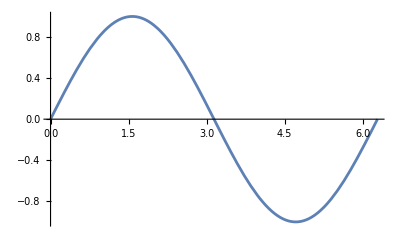

Show::gcomb: Could not combine the graphics objects in Show[,].

Show[-Graphics3D-,-Graphics-]

```mathematica
(*Define the 3D plot*)plot3D=Graphics[Plot3D[x^2+y^2,{x,-3,3},{y,-3,3},PlotStyle->Directive[Opacity[0.7],Blue]]]
plot2D=Graphics[Plot[Sin[t],{t,0,2 Pi}]]
(*Overlay the 2D plot on top of the 3D plot*)
Show[plot3D,plot2D]
```

```mathematica
(* Contour plot for the signed absolute log of the Ricci scalar: sign(R)Log|R| *)
p1=Rasterize[Show[
ContourPlot[If[y>branch1int[x],-Log[Abs[Ricci[x,y]]],None],{x,0,1},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",PlotRange->All,Contours->20,ContourStyle->None
,PlotRangePadding->None,Mesh->None,Frame->True,FrameLabel->{"x","τ"},
(*PlotLabel->"Ricci Scalar in D=4",*)
LabelStyle->Directive[16,Black,FontFamily->"Latin Modern Roman",Offset[{-10,0}]],FrameTicksStyle->Directive[Thickness[0.002],Black]],
ContourPlot[If[y<branch4int[x],-Log[Abs[Ricci[x,y]]],None],{x,0,1},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",Contours->20,ContourStyle->None],
ContourPlot[If[branch2int[x]>y>branch3int[x] ,-Log[Abs[Ricci[x,y]]],None],{x,0,1},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",Contours->20,ContourStyle->None],
ContourPlot[If[branch1int[x]>y>branch2int[x] ,Log[Abs[Ricci[x,y]]],None],{x,0,1},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",Contours->20,ContourStyle->None],
ContourPlot[If[branch3int[x]>y>branch4int[x] ,Log[Abs[Ricci[x,y]]],None],{x,0,1},{y,0,DeltaNow},PlotPoints->200,ColorFunction->"TemperatureMap",Contours->20,ContourStyle->None],
Plot[branch1int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch2int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch3int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch4int[x],{x,0,1},PlotStyle->{Thickness[0.005],Black}],
Plot[branch1int[xmin]+x*branch1int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch2int[xmin]+x*branch2int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch3int[xmin]+x*branch3int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}],
Plot[branch4int[xmin]+x*branch4int'[xmin],{x,0,0.3},PlotStyle->{Thickness[0.005],Red,Dashed}]
,AspectRatio->2/3],ImageResolution->300,ImageSize->400]
```

InterpolatingFunction::dmval: Input value {5.02513×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.98493} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.989955} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
p1=-Graphics-
```

-Graphics-

```mathematica
Export["RicciD4.pdf",p1]
```

RicciD4.pdf

{tau[x]→InterpolatingFunction[…][x]}

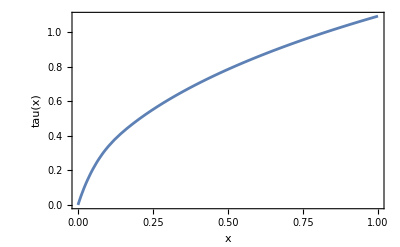

1.09213

```mathematica
(* geodesic equation *)
repltau=NDSolve[{tau'[x]==1/(x+fint[x,tau[x]]),tau[xmin]==0},tau[x],{x,xmin,xmax}][[1]]
p1=Plot[tau[x]/.repltau,{x,xmin,xmax},PlotRange->All,Frame->True,FrameLabel->{"x","tau(x)"}]
tau[x]/.repltau/.x->xmax
```